## Experimental

### TrackEcoEq

#### Definition

```mathematica
TrackEcoEq[pops:(_?VariablesQ),{trait_,traitmin_?NumericQ,traitmax_?NumericQ},opts___?OptionQ]:=

Module[{
func=FuncStyle["TrackEcoEq"],
(* options *)
verbose,verboseall,printtrace,monitor,
fixed,method,
(* other variables *)
nb,res,
fixedvars},

Block[{Nsp},

If[modelloaded≠True,Msg[EcoEvoGeneral::nomodel];Return[$Failed]];
If[Global`debug,Print["In ",func]];

(* handle options *)

verbose=Evaluate[Verbose/.Flatten[{opts,Options[TrackEcoEq]}]];
If[Global`debug,verbose=True];
verboseall=Evaluate[VerboseAll/.Flatten[{opts,Options[TrackEcoEq]}]];
If[verboseall,verbose=True];

printtrace=Evaluate[PrintTrace/.Flatten[{opts,Options[TrackEcoEq]}]];
monitor=Evaluate[Monitor/.Flatten[{opts,Options[TrackEcoEq]}]];

Return[res]

]];
```

#### Messages

```mathematica
TrackEcoEq::parvar=
"`1` cannot be used as a variable.";

TrackEcoEq::nosol=
"Could not find a solution at par=`1`, quitting.";
```

### TrackEcoEvoEq

#### Messages

```mathematica
TrackEcoEvoEq::parvar=
"`1` cannot be used as a variable.";

TrackEcoEvoEq::nosol=
"Could not find a solution at par=`1`, quitting.";

TrackEcoEvoEq::conv=
"Two species converged at par=`1`, quitting";
```

### EvoSim

```mathematica
Dynamic[{i,traits}]
```

```mathematica
(* try replacing progenitor – even faster?! *)
σa=0.3;
imax=1000;
verbose=False;

feaopts={Method->"EcoSim",TMax->10^12};
(*initial point*)
nsp=1;
traits={Subscript[x, 1]->-0.9};
pops=FindEcoAttractor[lv,traits,ICs->{Subscript[n, 1]->0.1},Evaluate[Sequence@@feaopts]];

(* storage *)
xresults={};
nresults={};

(* main loop *)
Do[
If[verbose,Print["i=",i]];
(* add to storage *)
Do[
AppendTo[xresults,{i,Subscript[x, sp]/.traits}];
AppendTo[nresults,{i,Subscript[n, sp]/.pops}];
,{sp,nsp}];
If[verbose,Print["traits=",traits]];
If[verbose,Print["eq=",eq]];

(* pick a species to mutate & generate mutant *)
(*sp′=RandomInteger[{1,nsp}];*)
sp′=RandomChoice[Table[Subscript[n, sp]/.pops,{sp,nsp}]->Table[sp,{sp,nsp}]];
xres=Subscript[x, sp′]/.traits;
xinv=xres+RandomReal[{-0.02,0.02}];

(* calculate invasion rate of mutant *)
inv=Inv[lv,traits,pops,Subscript[x, 0]->xinv];
If[verbose,Print["xinv=",xinv," inv=",inv]];

If[inv>0, (* if mutant can invade ... *)
(* replace xres with xinv and solve for eq *)
traits′=ReplacePart[traits,sp′->(Subscript[x, sp′]->xinv)];
eq′=FindEcoAttractor[lv,traits′,ICs->pops,Evaluate[Sequence@@feaopts]];
If[verbose,Print["eq′=",eq′]];

(* calculate invasion rate of xres back into eq′ *)
inv′=Inv[lv,traits′,eq′,Subscript[x, 0]->xres];
If[verbose,Print["inv′=",inv′]];

If[inv′>0, (* if xres can back invade *)
nsp=nsp+1;
traits′=Append[traits′,Subscript[x, nsp]->xres];
(*Print["mut inv at",traits′];*)
pops′=Append[pops,Subscript[n, nsp]->0.1];
eq′=FindEcoAttractor[lv,traits′,ICs->pops′,Evaluate[Sequence@@feaopts]];
];

(* check for extinct species *)
pos=Select[eq′,#⟦2⟧>10^-4&]⟦All,1,2⟧;
nsp′=Length[pos];
If[nsp′<nsp, (* extinction occured *)
traits=Table[Subscript[x, sp]->(Subscript[x, pos⟦sp⟧]/.traits′),{sp,nsp′}];
pops=Table[Subscript[n, sp]->(Subscript[n, pos⟦sp⟧]/.eq′),{sp,nsp′}];
nsp=nsp′
,
traits=traits′;
pops=eq′
];
];
,{i,imax}]
```

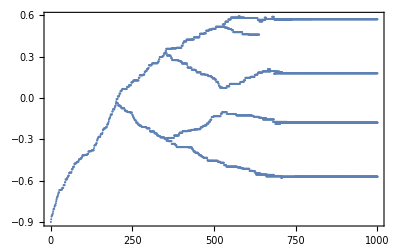

```mathematica
ListPlot[xresults,Frame->True,Axes->False]
```

```mathematica
(* track paths – not so good *)
σa=0.35;
imax=1000;
verbose=False;

feaopts={Method->"EcoSim",TMax->10^12};
(*initial point*)
nsp=1;
traits={Subscript[x, 1]->-0.9};
pops=FindEcoAttractor[lv,traits,ICs->{Subscript[n, 1]->0.1},Evaluate[Sequence@@feaopts]];

(* storage *)
xresults={};
nresults={};
xpath[1]={};
sppath[1]=1;
paths={1};
npaths=1;

(* main loop *)
Do[
If[verbose,Print["i=",i]];
(* add to storage *)
Do[
AppendTo[xresults,{i,Subscript[x, sp]/.traits}];
AppendTo[nresults,{i,Subscript[n, sp]/.pops}];
,{sp,nsp}];
Do[
AppendTo[xpath[path],{i,Subscript[x, sppath[path]]/.traits}];
,{path,paths}];
If[verbose,Print["traits=",traits]];
If[verbose,Print["eq=",eq]];

(* pick a species to mutate & generate mutant *)
(*sp′=RandomInteger[{1,nsp}];*)
sp′=RandomChoice[Table[Subscript[n, sp]/.pops,{sp,nsp}]->Table[sp,{sp,nsp}]];
xres=Subscript[x, sp′]/.traits;
xinv=xres+RandomReal[{-0.02,0.02}];

(* calculate invasion rate of mutant *)
inv=Inv[lv,traits,pops,Subscript[x, 0]->xinv];
If[verbose,Print["xinv=",xinv," inv=",inv]];

If[inv>0, (* if mutant can invade ... *)
(* replace xres with xinv and solve for eq *)
traits′=ReplacePart[traits,sp′->(Subscript[x, sp′]->xinv)];
eq′=FindEcoAttractor[lv,traits′,ICs->pops,Evaluate[Sequence@@feaopts]];
If[verbose,Print["eq′=",eq′]];

(* calculate invasion rate of xres back into eq′ *)
inv′=Inv[lv,traits′,eq′,Subscript[x, 0]->xres];
If[verbose,Print["inv′=",inv′]];

If[inv′>0, (* if xres can back invade *)
nsp=nsp+1;
traits′=Append[traits′,Subscript[x, nsp]->xres];
(* end old path *)
paths=DeleteCases[paths,sppath[sp′]];
(* start 2 new paths *)
xpath[npaths+1]=xpath[npaths+2]={};
sppath[npaths+1]=sp′;
sppath[npaths+2]=nsp;
paths=Join[paths,{npaths+1,npaths+2}];
npaths=npaths+2;
(*Print["mut inv at",traits′];*)
pops′=Append[pops,Subscript[n, nsp]->0.1];
eq′=FindEcoAttractor[lv,traits′,ICs->pops′,Evaluate[Sequence@@feaopts]];
];

(* check for extinct species *)
pos=Select[eq′,#⟦2⟧>10^-4&]⟦All,1,2⟧;
nsp′=Length[pos];
If[nsp′<nsp, (* extinction occured *)
traits=Table[Subscript[x, sp]->(Subscript[x, pos⟦sp⟧]/.traits′),{sp,nsp′}];
pops=Table[Subscript[n, sp]->(Subscript[n, pos⟦sp⟧]/.eq′),{sp,nsp′}];
nsp=nsp′
,
traits=traits′;
pops=eq′
];
];
,{i,imax}]
```

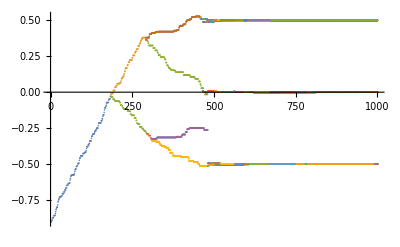

```mathematica
ListPlot[Table[xpath[p],{p,npaths}]]
```

```mathematica
npaths
```

105

```mathematica
traits
```

{x_1→0.571374,x_2→-0.179244,x_3→0.179244,x_4→-0.571745,x_5→-0.571234,x_6→0.178733}

```mathematica
?TemporalData
```

TemporalData[{v_1,v_2,…},tspec] represents temporal data with values v_i at times specified by tspec.
TemporalData[{{v_11,v_12,…},{v_21,v_22,…},…},tspec] represents a temporal data collection with values v_ij at times specified by tspec.
TemporalData[{{t_1,v_1},{t_2,v_2}…}] represents temporal data specified by time-value pairs {t_i,v_i}.
TemporalData[{{{t_11,v_11},{t_12,v_12}…},{{t_21,v_21},{t_22,v_22},…},…}] represents a temporal data collection given as lists of time-value pairs {t_ij,v_ij}.

```mathematica
?TreeGraph
```

RowBox[{"TreeGraph", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["u", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["u", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] yields a tree where SubscriptBox[StyleBox["u", "TI"], StyleBox["i", "TI"]] is the predecessor of SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] yields a tree with edges SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] yields a tree with vertices SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]] and edges SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["j", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] yields a tree with vertex and edge properties defined by the symbolic wrappers SubscriptBox[StyleBox["w", "TI"], StyleBox["k", "TI"]].
RowBox[{"TreeGraph", "[", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["j", "TI"]]}], ",", "…"}], "}"}], "]"}] uses rules RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], "→", SubscriptBox[StyleBox["v", "TI"], StyleBox["j", "TI"]]}] to specify a tree.

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

EcoEvo Package Version 0.9.3β (September 16, 2018)

$Aborted